```mathematica
Remove["Global`*"]
Needs["ErrorBarPlots`"]
```

```mathematica
data={{0.3,7},{40,8},{98.9,9}}
```

{{0.3,7},{40,8},{98.9,9}}

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[7.07057+0.0200308 x]

```mathematica
e=lm["FitResiduals"]
```

{-0.0765802,0.128197,-0.0516169}

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t Statistic | P-Value
1 | 7.07057 | 0.138707 | 50.975 | 0.0124873
x | 0.0200308 | 0.00225197 | 8.8948 | 0.0712728

```mathematica
e=Table[ErrorBar[i],{i,Abs[e]}]
```

{ErrorBar[Abs[ErrorBar[0.0765802]]],ErrorBar[Abs[ErrorBar[0.128197]]],ErrorBar[Abs[ErrorBar[0.0516169]]]}

```mathematica
e[[2]]
```

ErrorBar[0.128197]

```mathematica
data2=Table[{data[[i]],e[[i]]},{i,1,Length[e]}]
```

{{{0.3,7},ErrorBar[0.0765802]},{{40,8},ErrorBar[0.128197]},{{98.9,9},ErrorBar[0.0516169]}}

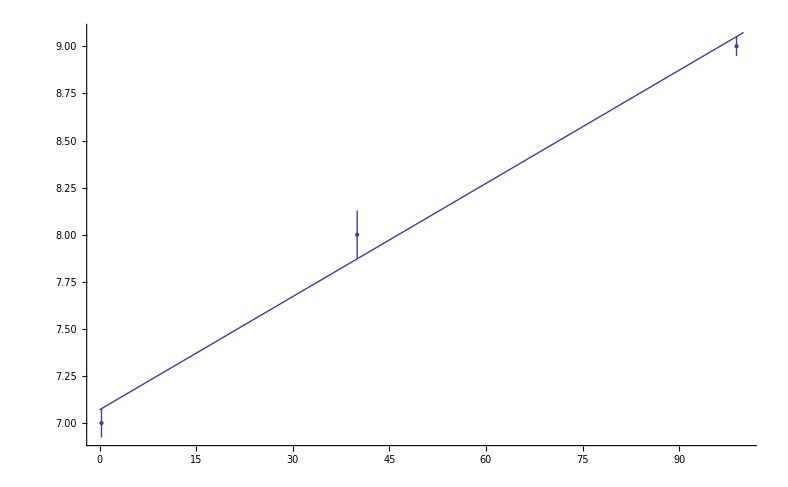

```mathematica
Show[ErrorListPlot[data2],Plot[lm[x],{x,0,100}]]
```